```mathematica
p1=7074;e1=0.05;p2=7748;e2=0.10;d=250000;
```

```mathematica
nudot[nu_,p_,e_] =Sqrt[1.0/p^3]*(1+e*Cos[nu])^2;
```

```mathematica
nux[nu_,p_,e_]=p/(1+e*Cos[nu*3.14/180])*Cos[nu*3.14/180];
```

```mathematica
nuy[nu_,p_,e_]=p/(1+e*Cos[nu*3.14/180])*Sin[nu*3.14/180];
```

```mathematica
distnu[nu1_,p1_,e1_,nu2_,p2_,e2_]=(nux[nu1,p1,e1]-nux[nu2,p2,e2])^2+(nuy[nu1,p1,e1]-nuy[nu2,p2,e2])^2;
```

```mathematica
flow=StreamPlot[{nudot[nu1,p1,e1],nudot[nu2,p2,e2]},{nu1,0,360},{nu2,0,360}];
```

```mathematica
rend=RegionPlot[Evaluate[distnu[nu1,p1,e1,nu2,p2,e2]]<=d,{nu1,0,360},{nu2,0,360}];
```

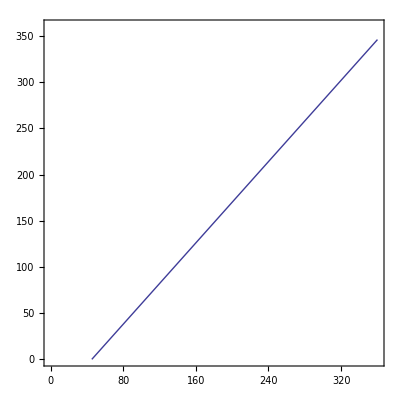

```mathematica
bar=ContourPlot[1.1 nu1-nu2==50,{nu1,0,360},{nu2,0,360}]
```

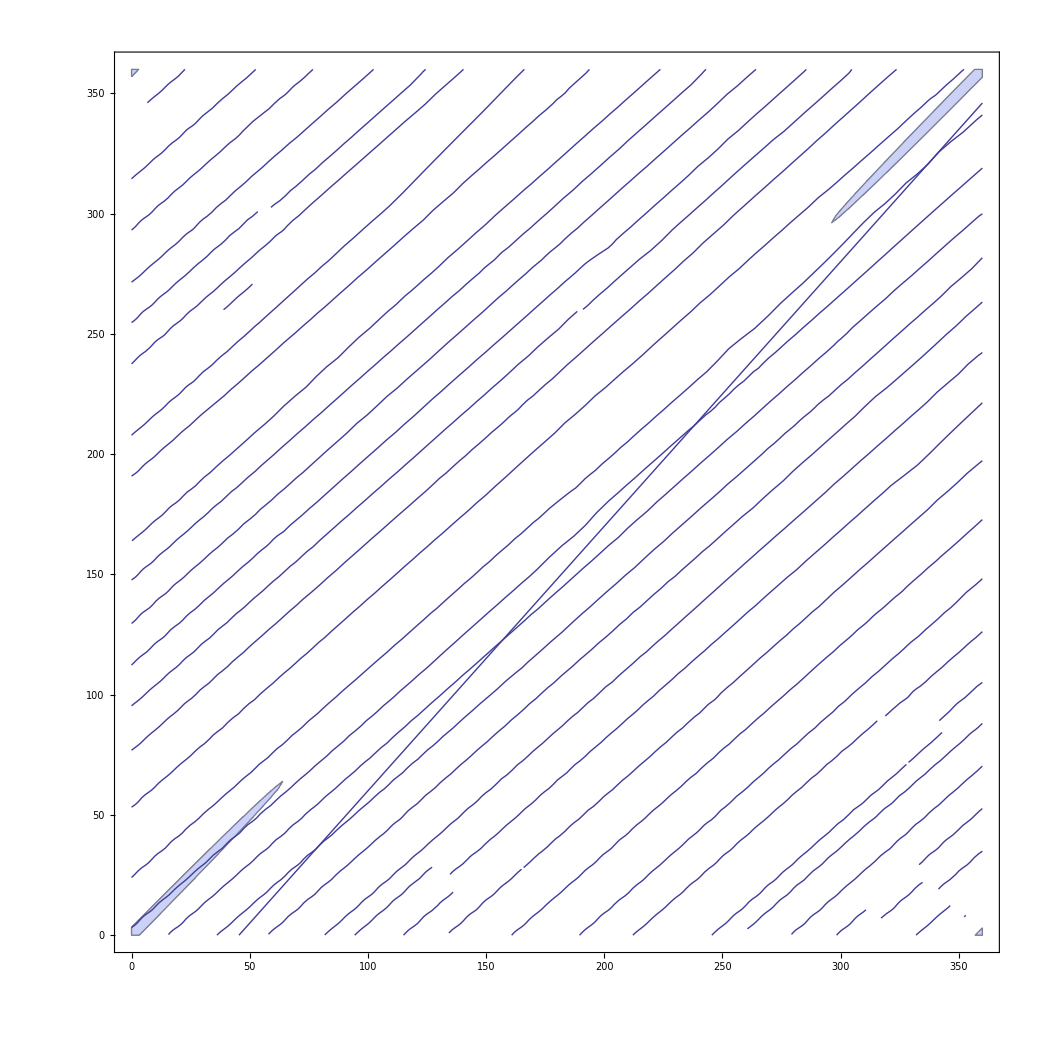

```mathematica
Show[rend,bar,plot]
```

```mathematica
test=((-7748*Sin[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Sin[0.0174444444444444*NU1]/(0.05*Cos[0.0174444444444444*NU1]+1))*(0.000414815151392623*(0.05*Cos[0.0174444444444444*NU1]+1)*Cos[0.0174444444444444*NU1]-0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU1]^2-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]^2)+(-7748*Cos[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Cos[0.0174444444444444*NU1]/(0.05*Cos[0.0174444444444444*NU1]+1))*(-0.000414815151392623*(0.05*Cos[0.0174444444444444*NU1]+1)*Sin[0.0174444444444444*NU1]+0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU1]*Cos[0.0174444444444444*NU1]-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2]))
```

((7074 Cos[0.0174444 NU1])/(1+0.05 Cos[0.0174444 NU1])-(7748 Cos[0.0174444 NU2])/(1+0.1 Cos[0.0174444 NU2])) (-0.000414815 (1+0.05 Cos[0.0174444 NU1]) Sin[0.0174444 NU1]+0.0000207408 Cos[0.0174444 NU1] Sin[0.0174444 NU1]+0.000396362 (1+0.1 Cos[0.0174444 NU2]) Sin[0.0174444 NU2]-0.0000396362 Cos[0.0174444 NU2] Sin[0.0174444 NU2])+((7074 Sin[0.0174444 NU1])/(1+0.05 Cos[0.0174444 NU1])-(7748 Sin[0.0174444 NU2])/(1+0.1 Cos[0.0174444 NU2])) (0.000414815 (1+0.05 Cos[0.0174444 NU1]) Cos[0.0174444 NU1]-0.000396362 (1+0.1 Cos[0.0174444 NU2]) Cos[0.0174444 NU2]+0.0000207408 Sin[0.0174444 NU1]^2-0.0000396362 Sin[0.0174444 NU2]^2)

```mathematica
Plot3D[test,{NU1,90,100},{NU2,0,150}]
```

-Graphics3D-

```mathematica
data=Table[{{nu1,nu2},{nudot[nu1,p1,e1],nudot[nu2,p2,e2]}},{nu1,0,360,0.5},{nu2,0,360,0.5}];
```

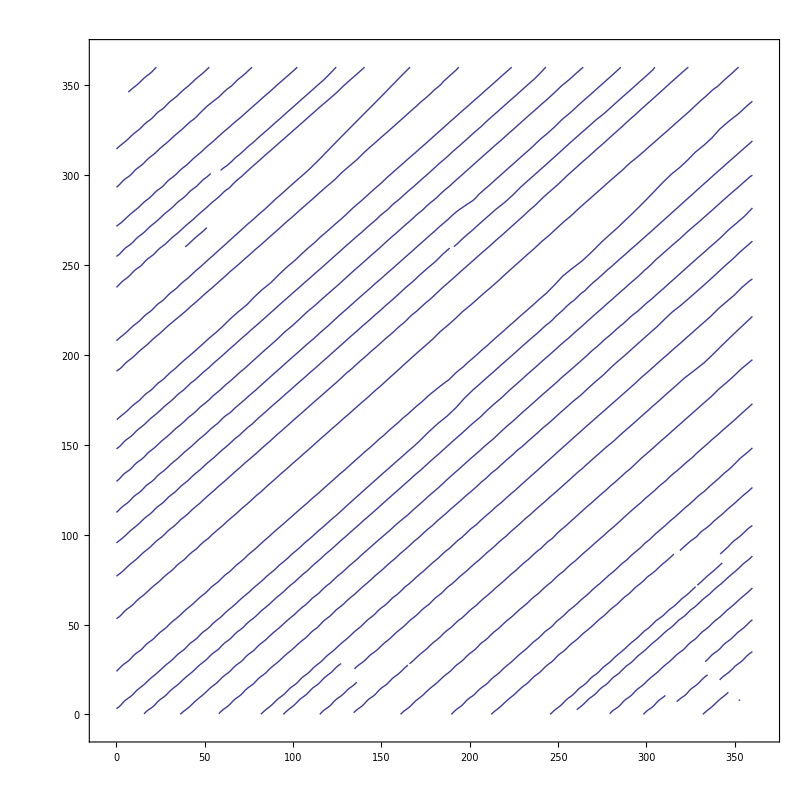

```mathematica
plot=ListStreamPlot[data,StreamStyle->"Line",PlotRangePadding->0]
```